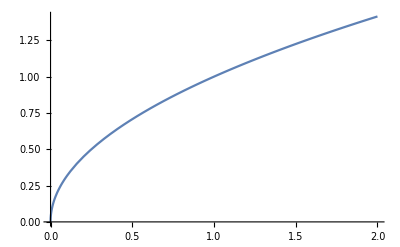

```mathematica
Plot[Sqrt[x],{x,0,2}]

Solve[{a+b==c+d,c+d==e+f,e+f==g+h,a+c==b+d,b+d==f+h,f+h==e+g},{a}]
```

```mathematica
Sqrt[4+4]
```

2 √2

```mathematica
Sqrt[4]
```

2

```mathematica
Sqrt[4]+Sqrt[4]<Sqrt[8]
```

```mathematica
False
Sqrt[1]+Sqrt[1]<Sqrt[2]
```

```mathematica
Sqrt[a/2]+Sqrt[b/2] ≤ Sqrt[a+b]
```

(√a)/(√2)+(√b)/(√2)≤√(a+b)

```mathematica
Sqrt[0.2]+Sqrt[0.2]<Sqrt[0.4]
```

False

```mathematica
Solve[{a+b == c+d == e+f == g+h==x, a+c==b+d==f+h==e+g=y},{a}]
```

Set::write: Tag Equal in a + b == c + d == e + f == g + h is Protected.

Set::write: Tag Equal in a + c == b + d == f + h == e + g is Protected.

Solve::naqs: x && y is not a quantified system of equations and inequalities.

Solve[{x,y},{a}]

```mathematica
M = {{1,1,0,0,0,0,0,0,a},{0,0,1,1,0,0,0,0,b},{0,0,0,0,1,1,0,0,c},{0,0,0,0,0,0,1,1,d},{1,0,1,0,0,0,0,0,e},{0,1,0,1,0,0,0,0,f},{0,0,0,0,1,0,1,0,g},{0,0,0,0,0,1,0,1,h},{1,1,1,1,1,1,1,1,1}}
```

{{1,1,0,0,0,0,0,0,a},{0,0,1,1,0,0,0,0,b},{0,0,0,0,1,1,0,0,c},{0,0,0,0,0,0,1,1,d},{1,0,1,0,0,0,0,0,e},{0,1,0,1,0,0,0,0,f},{0,0,0,0,1,0,1,0,g},{0,0,0,0,0,1,0,1,h},{1,1,1,1,1,1,1,1,1}}

```mathematica
MatrixForm[M]
```

```mathematica
({{1, 1, 0, 0, 0, 0, 0, 0, a}, {0, 0, 1, 1, 0, 0, 0, 0, b}, {0, 0, 0, 0, 1, 1, 0, 0, c}, {0, 0, 0, 0, 0, 0, 1, 1, d}, {1, 0, 1, 0, 0, 0, 0, 0, e}, {0, 1, 0, 1, 0, 0, 0, 0, f}, {0, 0, 0, 0, 1, 0, 1, 0, g}, {0, 0, 0, 0, 0, 1, 0, 1, h}, {1, 1, 1, 1, 1, 1, 1, 1, 1}})
```

```mathematica
RowReduce[M]
```

{{1,0,0,-1,0,0,0,0,0},{0,1,0,1,0,0,0,0,0},{0,0,1,1,0,0,0,0,0},{0,0,0,0,1,0,0,-1,0},{0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,1,1,0},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}

```mathematica
MatrixForm[%57]
```

(1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
({{1, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 1}, {1, 0, 1, 0, 0, 0, 0, 0}, {0, 1, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 1, 0}, {0, 0, 0, 0, 0, 1, 0, 1}, {1, 1, 1, 1, 1, 1, 1, 1}})

NullSpace[M]
```

{{1,1,0,0,0,0,0,0},{0,0,1,1,0,0,0,0},{0,0,0,0,1,1,0,0},{0,0,0,0,0,0,1,1},{1,0,1,0,0,0,0,0},{0,1,0,1,0,0,0,0},{0,0,0,0,1,0,1,0},{0,0,0,0,0,1,0,1},{1,1,1,1,1,1,1,1}}

{{0,0,0,0,1,-1,-1,1},{1,-1,-1,1,0,0,0,0}}

```mathematica
MatrixRank[M]
```

```mathematica
6
B = {a,a,a,a,b,b,b,b,1}
```

6

{a,a,a,a,b,b,b,b,1}

```mathematica
X = LinearSolve[M,B]
LinearSolve[{{1,3},{1,6}},{2,2}]
```

LinearSolve::nosol: Linear equation encountered that has no solution.

LinearSolve[{{1,1,0,0,0,0,0,0},{0,0,1,1,0,0,0,0},{0,0,0,0,1,1,0,0},{0,0,0,0,0,0,1,1},{1,0,1,0,0,0,0,0},{0,1,0,1,0,0,0,0},{0,0,0,0,1,0,1,0},{0,0,0,0,0,1,0,1},{1,1,1,1,1,1,1,1}},{a,a,a,a,b,b,b,b,1}]

{2,0}

```mathematica
{1,0}
```

```mathematica
RowReduce[M]
```

LinearSolve::nosol: Linear equation encountered that has no solution.

LinearSolve[{{1,1,0,0,0,0,0,0},{0,0,1,1,0,0,0,0},{0,0,0,0,1,1,0,0},{0,0,0,0,0,0,1,1},{1,0,1,0,0,0,0,0},{0,1,0,1,0,0,0,0},{0,0,0,0,1,0,1,0},{0,0,0,0,0,1,0,1},{1,1,1,1,1,1,1,1}},{a,b,c,d,e,f,g,h,1}]

{{1,0,0,-1,0,0,0,0},{0,1,0,1,0,0,0,0},{0,0,1,1,0,0,0,0},{0,0,0,0,1,0,0,-1},{0,0,0,0,0,1,0,1},{0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
MatrixForm[%25]
```

(1 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

{{0,0,0,0,1,-1,-1,1},{1,-1,-1,1,0,0,0,0}}

Rank[{{1,1,0,0,0,0,0,0},{0,0,1,1,0,0,0,0},{0,0,0,0,1,1,0,0},{0,0,0,0,0,0,1,1},{1,0,1,0,0,0,0,0},{0,1,0,1,0,0,0,0},{0,0,0,0,1,0,1,0},{0,0,0,0,0,1,0,1},{1,1,1,1,1,1,1,1}}]

LinearSolve::nosol: Linear equation encountered that has no solution.

LinearSolve[{{1,1,0,0,0,0,0,0},{0,0,1,1,0,0,0,0},{0,0,0,0,1,1,0,0},{0,0,0,0,0,0,1,1},{1,0,1,0,0,0,0,0},{0,1,0,1,0,0,0,0},{0,0,0,0,1,0,1,0},{0,0,0,0,0,1,0,1}},{a,b,c,d,e,f,g,h}]

```mathematica
LinearSolve[{{1,1,0,0,0,0,0,0},{0,0,1,1,0,0,0,0},{0,0,0,0,1,1,0,0},{0,0,0,0,0,0,1,1},{1,0,1,0,0,0,0,0},{0,1,0,1,0,0,0,0},{0,0,0,0,1,0,1,0},{0,0,0,0,0,1,0,1},{1,1,1,1,1,1,1,1}},{a,b,c,d,e,f,g,h,z}]
```

LinearSolve::nosol: Linear equation encountered that has no solution.

LinearSolve[{{1,1,0,0,0,0,0,0},{0,0,1,1,0,0,0,0},{0,0,0,0,1,1,0,0},{0,0,0,0,0,0,1,1},{1,0,1,0,0,0,0,0},{0,1,0,1,0,0,0,0},{0,0,0,0,1,0,1,0},{0,0,0,0,0,1,0,1},{1,1,1,1,1,1,1,1}},{a,b,c,d,e,f,g,h,z}]

```mathematica
A = {{1,-2,-1},{-3,1,9},{-1,7,-5}}
```

{{1,-2,-1},{-3,1,9},{-1,7,-5}}

```mathematica
MatrixForm[A]
```

(1 | -2 | -1
-3 | 1 | 9
-1 | 7 | -5)

```mathematica
NullSpace[A]
```

{{17,6,5}}

```mathematica
NullSpace[{{1,0},{0,1}}]
```

```mathematica
{}
A = {{1,1,-1,-1,0,0,0,0},{0,0,1,1,-1,-1,0,0},{0,0,0,0,1,1,-1,-1},{1,-1,1,-1,0,0,0,0},{0,1,0,1,0,-1,0,-1},{0,0,0,0,-1,1,-1,1},{1,1,1,1,1,1,1,1}}
```

{}

{{1,1,-1,-1,0,0,0,0},{0,0,1,1,-1,-1,0,0},{0,0,0,0,1,1,-1,-1},{1,-1,1,-1,0,0,0,0},{0,1,0,1,0,-1,0,-1},{0,0,0,0,-1,1,-1,1},{1,1,1,1,1,1,1,1}}

```mathematica
MatrixForm[A]
```

```mathematica
({{1, 1, -1, -1, 0, 0, 0, 0}, {0, 0, 1, 1, -1, -1, 0, 0}, {0, 0, 0, 0, 1, 1, -1, -1}, {1, -1, 1, -1, 0, 0, 0, 0}, {0, 1, 0, 1, 0, -1, 0, -1}, {0, 0, 0, 0, -1, 1, -1, 1}, {1, 1, 1, 1, 1, 1, 1, 1}})
b = {b1,b2,b3,b4,b5,b6,b7,b8}
```

{{1,1,-1,-1,0,0,0,0},{0,0,1,1,-1,-1,0,0},{0,0,0,0,1,1,-1,-1},{1,-1,1,-1,0,0,0,0},{0,1,0,1,0,-1,0,-1},{0,0,0,0,-1,1,-1,1},{1,1,1,1,1,1,1,1}}

{b1,b2,b3,b4,b5,b6,b7,b8}

```mathematica
NullSpace[A]
```

```mathematica
LinearSolve[A,{0,0,0,0,0,0,1}]
```

{0,1/4,1/4,0,0,1/4,1/4,0}

```mathematica
PadRight[A]
```

{{1,1,-2,0,0,0,0,0},{0,0,1,1,-1,-1,0,0},{0,0,0,0,1,1,-1,-1},{1,-1,1,-1,0,0,0,0},{0,1,0,1,0,-1,0,-1},{0,0,0,0,-1,1,-1,1},{1,1,1,1,1,1,1,1}}